```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/00_SplinePack-034.nb"]//Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]]//Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]]//Quiet;


Clear[SavitzkyGolayFilterExtended]


SavitzkyGolayFilterExtended[DOrder_,M_,nl_,nr_,data_] := Module[{i,j,p,t},
p = Table[t^i,{i,0,M}];
j = nl+nr+1;
i = Range[j];
Join[
D[Fit[Transpose[{i,Take[data,   j]}],p,t],{t,DOrder}]/.t->Take[i,  nl],
SavitzkyGolayFilter[DOrder,M,nl,nr,data],
D[Fit[Transpose[{i,Take[data,-j]}],p,t],{t,DOrder}]/.t->Take[i,-nr]]];



Clear[
ParamPadToTake,
ParamTakeToPad]


ParamPadToTake[ImgDim_,LeftRightBottomTop_] := {
{LeftRightBottomTop[[2,2]]+1,If[ListQ[ImgDim],ImgDim[[2]],-1]-LeftRightBottomTop[[2,1]]},
{LeftRightBottomTop[[1,1]]+1,If[ListQ[ImgDim],ImgDim[[1]],-1]-LeftRightBottomTop[[1,2]]}};


ParamTakeToPad[ImgDim_,RowsCols_] := Module[{LeftRightBottomTop},
LeftRightBottomTop = Reverse[RowsCols];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[1]] -= 1;
LeftRightBottomTop[[2]] = ImgDim-LeftRightBottomTop[[2]];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[2]] = Reverse[LeftRightBottomTop[[2]]];
LeftRightBottomTop];



Clear[
LoadFromTIF,
SaveAsTIF]


LoadFromTIF[CheckBitLength_,fname_] := Module[{X},
X = Import[fname];
X[[-1]] = ReadQRCode[X[[-1]]];
If[
If[TrueQ[CheckBitLength],
SameQ[
Piecewise[{{1,#≤1},{8,1<#≤8}},16]&/@Ceiling[Log[2,X[[-1,1]]]],
Ceiling[Log[2,Map[Length[Union@@ImageData[#]]&,Drop[X,-1]]]]],
True],
X[[-1]] = X[[-1,2]];
Fold[
ReplacePart[#1,#2[[1]],#2[[2]]]&,
X[[-1]],
Transpose[
{Drop[X,-1],
Position[X[[-1]],Image]}]]]];


SaveAsTIF[fname_,data_] := Module[{x,X},
X = data/.x_:>MyVectorPlaceholder/;ImageQ[x];
X = Append[
Extract[data,Position[X,MyVectorPlaceholder]],
X/.MyVectorPlaceholder->Image];
X[[-1]] = {Map[Length[Union@@ImageData[#]]&,Drop[X,-1]],X[[-1]]};
X[[-1]] = WriteQRCode[X[[-1]]];
MDExport[fname,X,"ImageEncoding"->"LZW"]];



Clear[ChangeImgDims]


ChangeImgDims[
  B_?ImageQ,
nx_?IntegerQ,
ny_?IntegerQ,
padding_] := Module[{R,x,y},
{x,y} = {nx,ny}-ImageDimensions[R=B];
If[y<0,
y = {Quotient[-y,2],-y};
y = {First[y],Subtract@@y}+{1,-1};
R = ImageTake[R,y],
If[y>0,
y = {y,Quotient[y,2]};
y = {Last[y],Subtract@@y};
R = ImagePad[R,{{0,0},y},padding]]];
If[x<0,
x = {Quotient[-x,2],-x};
x = {First[x],Subtract@@x}+{1,-1};
R = ImageTake[R,All,x],
If[x>0,
x = {x,Quotient[x,2]};
x = {Last[x],Subtract@@x};
R = ImagePad[R,{x,{0,0}},padding]]];
R];
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

```mathematica
$HistoryLength = 10;
PrependTo[MyTS,FontSize->24];
DatenOrdner = OutPath=NotebookDirectory[]~~"output directory\\";
```

```mathematica
FileExistsQ[DatenOrdner]
```

True

```mathematica
(*    aus Aerosol 0108.nb    *)

M = {"C2"->{"age"->28.,"sex"->"m","height"->174.,"weight"->75.,"beard"->"full","resp_dis"->"","nic_abu"->"abu","exper"->20.},"S1"->{"age"->26.,"sex"->"f","height"->172.,"weight"->56.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S2"->{"age"->27.,"sex"->"m","height"->181.,"weight"->64.,"beard"->"full","resp_dis"->"","nic_abu"->"","exper"->""},"S3"->{"age"->20.,"sex"->"d","height"->170.,"weight"->75.,"beard"->"","resp_dis"->"Asthma bronchiale (aktuell nicht exazerbiert)","nic_abu"->"","exper"->""},"S4"->{"age"->30.,"sex"->"f","height"->173.,"weight"->59.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S5"->{"age"->30.,"sex"->"m","height"->180.,"weight"->75.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S6"->{"age"->29.,"sex"->"f","height"->165.,"weight"->58.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S7"->{"age"->27.,"sex"->"f","height"->163.,"weight"->51.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S8"->{"age"->28.,"sex"->"f","height"->162.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S9"->{"age"->30.,"sex"->"m","height"->169.,"weight"->68.,"beard"->"full","resp_dis"->"","nic_abu"->"","exper"->""},"S10"->{"age"->52.,"sex"->"m","height"->183.,"weight"->80.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->""},"S11"->{"age"->66.,"sex"->"m","height"->183.,"weight"->70.,"beard"->"full","resp_dis"->"allergisches Asthma (saisonal)","nic_abu"->"","exper"->""},"S12"->{"age"->26.,"sex"->"m","height"->173.,"weight"->84.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->""},"O2"->{"age"->63.,"sex"->"f","height"->156.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->50.},"O3"->{"age"->56.,"sex"->"f","height"->170.,"weight"->76.,"beard"->"","resp_dis"->"","nic_abu"->"s.p.","exper"->44.},"O4"->{"age"->53.,"sex"->"f","height"->183.,"weight"->72.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->40.},"O5"->{"age"->54.,"sex"->"f","height"->171.,"weight"->70.,"beard"->"","resp_dis"->"","nic_abu"->"s.p.","exper"->43.},"O6"->{"age"->45.,"sex"->"m","height"->185.,"weight"->90.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->34.},"O7"->{"age"->64.,"sex"->"m","height"->187.,"weight"->82.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->40.},"O8"->{"age"->53.,"sex"->"m","height"->203.,"weight"->92.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->40.},"O9"->{"age"->24.,"sex"->"f","height"->160.,"weight"->58.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->14.},"O10"->{"age"->45.,"sex"->"m","height"->186.,"weight"->85.,"beard"->"3d","resp_dis"->"","nic_abu"->"abu","exper"->30.},"O11"->{"age"->65.,"sex"->"m","height"->176.,"weight"->63.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->55.},"O12"->{"age"->42.,"sex"->"m","height"->189.,"weight"->90.,"beard"->"","resp_dis"->"","nic_abu"->"abu","exper"->30.},"F1"->{"age"->63.,"sex"->"m","height"->186.,"weight"->88.,"beard"->"","resp_dis"->"","nic_abu"->"abu","exper"->50.},"F2"->{"age"->47.,"sex"->"f","height"->161.,"weight"->74.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->35.},"F3"->{"age"->47.,"sex"->"f","height"->158.,"weight"->72.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->38.},"F4"->{"age"->68.,"sex"->"f","height"->158.,"weight"->95.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->58.},"F5"->{"age"->63.,"sex"->"f","height"->172.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->53.},"F6"->{"age"->26.,"sex"->"f","height"->166.,"weight"->75.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->15.},"F7"->{"age"->50.,"sex"->"f","height"->156.,"weight"->54.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->39.},"F9"->{"age"->64.,"sex"->"f","height"->164.,"weight"->65.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->50.},"F10"->{"age"->26.,"sex"->"f","height"->168.,"weight"->65.,"beard"->"","resp_dis"->"","nic_abu"->"s.p.","exper"->20.},"F11"->{"age"->29.,"sex"->"f","height"->165.,"weight"->57.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->16.},"F12"->{"age"->33.,"sex"->"f","height"->178.,"weight"->80.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->28.},"F13"->{"age"->52.,"sex"->"f","height"->167.,"weight"->60.,"beard"->"","resp_dis"->"allergisches Asthma","nic_abu"->"","exper"->40.},"F14"->{"age"->38.,"sex"->"f","height"->165.,"weight"->66.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->27.},"F15"->{"age"->59.,"sex"->"f","height"->163.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->40.},"F16"->{"age"->37.,"sex"->"m","height"->180.,"weight"->76.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->27.},"F17"->{"age"->23.,"sex"->"f","height"->173.,"weight"->56.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->11.},"F18"->{"age"->56.,"sex"->"m","height"->180.,"weight"->80.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->45.},"F19"->{"age"->64.,"sex"->"f","height"->167.,"weight"->50.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->50.},"F20"->{"age"->46.,"sex"->"f","height"->168.,"weight"->61.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->35.},"T1"->{"age"->26.,"sex"->"m","height"->182.,"weight"->90.,"beard"->"full","resp_dis"->"","nic_abu"->"","exper"->""}};
```

```mathematica
Clear[ToEnglish,Z,newID]
{ToEnglish,Z} = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/EmissionRatePlotData.dat"]];
newID=Map[#[[1]]->StringJoin["P",ToString@#[[2]]]&,Transpose@{Union[Drop[Z[[All,1]],2]],Table[n,{n,Length@Union[Drop[Z[[All,1]],2]]}]}];
```

```mathematica
Z = Transpose[Join[Transpose[Z],Transpose[Join[
{{"Weight (kg)","Height (cm)","Sex","Experience (years)"},{"","","",""}},
  {"weight"            ,"height"            ,"sex","exper"                              }/.((First/@Drop[Z,2])/.M)]]]];
```

```mathematica
Z[[All,1]]=Z[[All,1]]/.newID;
TableForm[Z]
Length[Z]
```

Proband | Instrument | Task | Begin (s) | End (s) | Emission rate (P/s) | ER σ (P/s) | Water emission (mg/s) | Particles/Water (P/mg) | Weight (kg) | Height (cm) | Sex | Experience (years)
 |  |  |  |  |  |  |  |  |  |  |  | 
P1 | C | Breathing | 6206 | 7408 | -98 | 171 | 6.35133 | -15.4298 | 75. | 174. | m | 20.
P1 | C | Playing | 1200 | 2408 | 355 | 261 | 19.6555 | 18.0611 | 75. | 174. | m | 20.
P1 | C | Playing With Surgical Mask | 8449 | 9061 | 790 | 764 | 7.36465 | 107.269 | 75. | 174. | m | 20.
P1 | C | Speaking | 4010 | 5236 | 22 | 100 | 8.70055 | 2.52858 | 75. | 174. | m | 20.
P32 | S | Breathing | 3340 | 4555 | 228 | 153 |  |  | 56. | 172. | f | 
P32 | S | Speaking | 1200 | 2405 | 89 | 94 |  |  | 56. | 172. | f | 
P32 | S | Speaking With Surgical Mask | 5466 | 6682 | -122 | 196 |  |  | 56. | 172. | f | 
P36 | S | Speaking With Surgical Mask | 4524 | 5723 | -1 | 184 | 4.8826 | -0.204809 | 64. | 181. | m | 
P37 | S | Breathing | 4051 | 5256 | -157 | 302 | 8.03068 | -19.55 | 75. | 170. | d | 
P37 | S | Speaking | 7443 | 8659 | 590 | 162 | 5.92732 | 99.5391 | 75. | 170. | d | 
P37 | S | Speaking With Surgical Mask | 1200 | 2408 | 666 | 215 | 5.7454 | 115.919 | 75. | 170. | d | 
P38 | S | Speaking | 5299 | 6523 | -137 | 198 | 5.18286 | -26.4333 | 59. | 173. | f | 
P38 | S | Speaking With Surgical Mask | 424 | 1648 | 78 | 93 | 6.08984 | 12.8082 | 59. | 173. | f | 
P39 | S | Speaking With Surgical Mask | 876 | 2098 | -50 | 107 | 5.95228 | -8.40014 | 75. | 180. | m | 
P40 | S | Breathing | 4106 | 5320 | -199 | 335 | 8.3125 | -23.9398 | 58. | 165. | f | 
P40 | S | Speaking | 1869 | 3080 | 16 | 189 | 17.5803 | 0.910107 | 58. | 165. | f | 
P40 | S | Speaking With Surgical Mask | 6825 | 8040 | 114 | 267 | 5.6046 | 20.3404 | 58. | 165. | f | 
P41 | S | Breathing | 3261 | 4466 | -105 | 151 | 3.11025 | -33.7593 | 51. | 163. | f | 
P41 | S | Speaking | 5840 | 7058 | -260 | 312 | 5.79921 | -44.8337 | 51. | 163. | f | 
P41 | S | Speaking With Surgical Mask | 1200 | 2405 | 473 | 83 | 6.94787 | 68.0784 | 51. | 163. | f | 
P42 | S | Breathing | 3646 | 4851 | 48 | 164 | 3.95646 | 12.1321 | 55. | 162. | f | 
P42 | S | Speaking | 7694 | 8906 | 203 | 327 | 4.58863 | 44.2398 | 55. | 162. | f | 
P42 | S | Speaking With Surgical Mask | 1200 | 2440 | -163 | 249 | 9.10583 | -17.9006 | 55. | 162. | f | 
P43 | S | Breathing | 3656 | 4859 | 455 | 302 | 8.05346 | 56.4975 | 68. | 169. | m | 
P43 | S | Speaking | 7093 | 8303 | 1605 | 305 | 8.3908 | 191.281 | 68. | 169. | m | 
P43 | S | Speaking With Surgical Mask | 1200 | 2403 | 586 | 610 | 10.1777 | 57.5767 | 68. | 169. | m | 
P33 | S | Breathing | 4239 | 5441 | 296 | 224 | 8.28801 | 35.7142 | 80. | 183. | m | 
P33 | S | Playing | 10644 | 11848 | 2122 | 605 | 12.8713 | 164.863 | 80. | 183. | m | 
P33 | S | Speaking | 7057 | 8273 | 242 | 209 | 8.4451 | 28.6557 | 80. | 183. | m | 
P33 | S | Speaking With Surgical Mask | 1200 | 2408 | 947 | 475 | 18.7504 | 50.5057 | 80. | 183. | m | 
P34 | S | Breathing | 3418 | 4622 | 559 | 443 | 9.5607 | 58.4685 | 70. | 183. | m | 
P34 | S | Speaking | 5828 | 7040 | 1671 | 207 | 9.96255 | 167.728 | 70. | 183. | m | 
P34 | S | Speaking With Surgical Mask | 944 | 2159 | 2 | 413 | 9.34569 | 0.214002 | 70. | 183. | m | 
P35 | S | Breathing | 4027 | 5230 | -44 | 210 | 12.5258 | -3.51274 | 84. | 173. | m | 
P35 | S | Playing | 10374 | 11579 | 1355 | 428 | 16.1923 | 83.682 | 84. | 173. | m | 
P35 | S | Speaking | 7275 | 8480 | 481 | 229 | 8.78184 | 54.7721 | 84. | 173. | m | 
P35 | S | Speaking With Surgical Mask | 1093 | 2317 | 970 | 160 | 16.4966 | 58.8001 | 84. | 173. | m | 
P24 | O | Breathing | 6157 | 7360 | -48 | 198 | 5.04529 | -9.51383 | 55. | 156. | f | 50.
P24 | O | Playing | 1828 | 3032 | 838 | 288 | 19.4271 | 43.1356 | 55. | 156. | f | 50.
P24 | O | Playing With Surgical Mask | 8546 | 9159 | 320 | 568 | 8.02528 | 39.874 | 55. | 156. | f | 50.
P24 | O | Speaking | 4113 | 5328 | -245 | 356 | 8.90999 | -27.4972 | 55. | 156. | f | 50.
P25 | O | Breathing | 5900 | 7104 | 23 | 166 | 5.18188 | 4.43854 | 76. | 170. | f | 44.
P25 | O | Playing | 1200 | 2400 | 466 | 115 | 21.9253 | 21.254 | 76. | 170. | f | 44.
P25 | O | Playing With Surgical Mask | 8292 | 8912 | 215 | 400 | 9.70404 | 22.1557 | 76. | 170. | f | 44.
P25 | O | Speaking | 3515 | 4735 | 56 | 307 | 8.71046 | 6.42905 | 76. | 170. | f | 44.
P25 | O | Speaking With Surgical Mask | 10570 | 11789 | -164 | 273 | 4.28641 | -38.2605 | 76. | 170. | f | 44.
P26 | O | Breathing | 6226 | 7429 | 93 | 95 | 5.80198 | 16.029 | 72. | 183. | f | 40.
P26 | O | Playing | 1200 | 2427 | 1309 | 210 | 16.382 | 79.9047 | 72. | 183. | f | 40.
P26 | O | Playing With Surgical Mask | 8482 | 9086 | 911 | 612 | 6.44717 | 141.302 | 72. | 183. | f | 40.
P26 | O | Speaking | 3697 | 4929 | 189 | 114 | 6.88974 | 27.4321 | 72. | 183. | f | 40.
P26 | O | Speaking With Surgical Mask | 10224 | 11456 | -66 | 142 | 4.88131 | -13.521 | 72. | 183. | f | 40.
P27 | O | Speaking | 3109 | 4303 | -164 | 319 | 11.3842 | -14.4059 | 70. | 171. | f | 43.
P28 | O | Breathing | 6070 | 7281 | 117 | 304 | 9.31335 | 12.5626 | 90. | 185. | m | 34.
P28 | O | Playing | 1200 | 2429 | 521 | 316 | 35.627 | 14.6238 | 90. | 185. | m | 34.
P28 | O | Playing With Surgical Mask | 8842 | 9451 | 1610 | 483 | 9.25584 | 173.944 | 90. | 185. | m | 34.
P28 | O | Speaking | 3683 | 4905 | 257 | 227 | 14.3611 | 17.8955 | 90. | 185. | m | 34.
P29 | O | Breathing | 6229 | 7432 | 181 | 223 | 9.50645 | 19.0397 | 82. | 187. | m | 40.
P29 | O | Playing | 1200 | 2433 | 2535 | 195 | 34.9787 | 72.4727 | 82. | 187. | m | 40.
P29 | O | Playing With Surgical Mask | 8409 | 9017 | 670 | 238 | 13.4193 | 49.9282 | 82. | 187. | m | 40.
P29 | O | Speaking | 3689 | 4894 | 715 | 296 | 18.8318 | 37.9676 | 82. | 187. | m | 40.
P30 | O | Breathing | 7834 | 9039 | -187 | 432 | 7.19722 | -25.9823 | 92. | 203. | m | 40.
P30 | O | Playing | 1569 | 2777 | 1229 | 147 | 32.4661 | 37.8549 | 92. | 203. | m | 40.
P30 | O | Playing With Surgical Mask | 10204 | 10835 | 1053 | 273 | 15.7934 | 66.6734 | 92. | 203. | m | 40.
P30 | O | Speaking | 5280 | 6512 | -175 | 294 | 9.94692 | -17.5934 | 92. | 203. | m | 40.
P31 | O | Breathing | 6075 | 7278 | -145 | 266 | 5.34168 | -27.145 | 58. | 160. | f | 14.
P31 | O | Playing | 1200 | 2404 | 1645 | 461 | 22.9649 | 71.6312 | 58. | 160. | f | 14.
P31 | O | Playing With Surgical Mask | 8431 | 9042 | 1589 | 534 | 14.8384 | 107.087 | 58. | 160. | f | 14.
P31 | O | Speaking | 4015 | 5222 | 9 | 191 | 7.94626 | 1.13261 | 58. | 160. | f | 14.
P21 | O | Playing | 1200 | 2402 | 218 | 185 | 17.797 | 12.2493 | 85. | 186. | m | 30.
P21 | O | Playing With Surgical Mask | 8608 | 9211 | -209 | 268 | 17.5343 | -11.9195 | 85. | 186. | m | 30.
P21 | O | Speaking | 3747 | 4961 | -3 | 148 | 11.8492 | -0.253182 | 85. | 186. | m | 30.
P21 | O | Speaking With Surgical Mask | 10242 | 11447 | -136 | 279 | 10.1543 | -13.3933 | 85. | 186. | m | 30.
P22 | O | Breathing | 5645 | 6848 | 21 | 244 | 7.20408 | 2.91501 | 63. | 176. | m | 55.
P22 | O | Playing | 1032 | 2258 | 1484 | 211 | 26.5107 | 55.9774 | 63. | 176. | m | 55.
P22 | O | Playing With Surgical Mask | 8124 | 8741 | 1263 | 1224 | 10.8125 | 116.809 | 63. | 176. | m | 55.
P22 | O | Speaking | 3379 | 4595 | 144 | 409 | 13.1723 | 10.932 | 63. | 176. | m | 55.
P23 | O | Breathing | 6274 | 7483 | -150 | 196 | 8.32992 | -18.0074 | 90. | 189. | m | 30.
P23 | O | Playing | 1200 | 2411 | 660 | 274 | 24.5285 | 26.9075 | 90. | 189. | m | 30.
P23 | O | Playing With Surgical Mask | 8782 | 9386 | 894 | 620 | 14.5733 | 61.3453 | 90. | 189. | m | 30.
P23 | O | Speaking | 3565 | 4770 | 725 | 128 | 12.7055 | 57.0621 | 90. | 189. | m | 30.
P2 | F | Breathing | 5183 | 6376 | 48 | 35 | 6.17609 | 7.7719 | 88. | 186. | m | 50.
P2 | F | Playing | 1200 | 2392 | 1434 | 366 | 26.468 | 54.1787 | 88. | 186. | m | 50.
P2 | F | Speaking | 3057 | 4260 | 641 | 384 | 11.7497 | 54.5544 | 88. | 186. | m | 50.
P2 | F | Speaking With Surgical Mask | 6929 | 8125 | 447 | 189 | 8.23895 | 54.2545 | 88. | 186. | m | 50.
P13 | F | Breathing | 6063 | 7278 | 119 | 151 | 7.49066 | 15.8865 | 74. | 161. | f | 35.
P13 | F | Playing | 1379 | 2586 | 343 | 486 | 29.3035 | 11.7051 | 74. | 161. | f | 35.
P13 | F | Speaking | 3612 | 4826 | 63 | 92 | 14.9865 | 4.20379 | 74. | 161. | f | 35.
P15 | F | Breathing | 3293 | 4493 | 39 | 213 |  |  | 72. | 158. | f | 38.
P15 | F | Playing | 1588 | 2755 | 57 | 175 |  |  | 72. | 158. | f | 38.
P15 | F | Speaking | 4983 | 6228 | -144 | 175 |  |  | 72. | 158. | f | 38.
P15 | F | Speaking With Surgical Mask | 7425 | 8615 | 455 | 293 |  |  | 72. | 158. | f | 38.
P16 | F | Breathing | 5604 | 6813 | -2 | 317 | 8.18271 | -0.244418 | 95. | 158. | f | 58.
P16 | F | Playing | 1200 | 2405 | 2318 | 644 | 27.4037 | 84.587 | 95. | 158. | f | 58.
P16 | F | Speaking | 3543 | 4759 | -79 | 366 | 13.6893 | -5.77093 | 95. | 158. | f | 58.
P16 | F | Speaking With Surgical Mask | 7928 | 9141 | 432 | 245 | 6.09656 | 70.8597 | 95. | 158. | f | 58.
P17 | F | Playing | 1200 | 2401 | 1143 | 206 | 21.095 | 54.1834 | 55. | 172. | f | 53.
P17 | F | Speaking | 4001 | 5223 | -80 | 174 | 6.67978 | -11.9764 | 55. | 172. | f | 53.
P17 | F | Speaking With Surgical Mask | 8298 | 9499 | -89 | 291 | 5.70864 | -15.5904 | 55. | 172. | f | 53.
P18 | F | Breathing | 4996 | 6211 | 350 | 175 | 12.8319 | 27.2759 | 75. | 166. | f | 15.
P18 | F | Playing | 1200 | 2416 | 635 | 128 |  |  | 75. | 166. | f | 15.
P18 | F | Speaking | 3159 | 4364 | 7 | 67 | 23.5479 | 0.297266 | 75. | 166. | f | 15.
P19 | F | Breathing | 5401 | 6604 | -1 | 79 |  |  | 54. | 156. | f | 39.
P19 | F | Playing | 1200 | 2420 | 1171 | 176 |  |  | 54. | 156. | f | 39.
P19 | F | Speaking | 3399 | 4611 | 129 | 256 |  |  | 54. | 156. | f | 39.
P19 | F | Speaking With Surgical Mask | 7200 | 8407 | 486 | 220 |  |  | 54. | 156. | f | 39.
P20 | F | Breathing | 5911 | 7119 | 274 | 317 | 4.31308 | 63.5277 | 65. | 164. | f | 50.
P20 | F | Playing | 1200 | 2404 | 799 | 307 | 8.14177 | 98.1359 | 65. | 164. | f | 50.
P20 | F | Speaking | 3521 | 4759 | -121 | 140 | 5.55579 | -21.7791 | 65. | 164. | f | 50.
P20 | F | Speaking With Surgical Mask | 8075 | 9283 | 474 | 368 | 5.38106 | 88.0868 | 65. | 164. | f | 50.
P3 | F | Playing | 1200 | 2398 | 11 | 288 |  |  | 65. | 168. | f | 20.
P3 | F | Speaking | 3145 | 4340 | 5 | 203 | 18.3802 | 0.272032 | 65. | 168. | f | 20.
P3 | F | Speaking With Surgical Mask | 6889 | 8093 | 943 | 173 | 5.75107 | 163.97 | 65. | 168. | f | 20.
P4 | F | Breathing | 5914 | 7118 | 149 | 368 | 3.98727 | 37.3689 | 57. | 165. | f | 16.
P4 | F | Playing | 1200 | 2413 | 15 | 313 | 18.7977 | 0.797972 | 57. | 165. | f | 16.
P5 | F | Breathing | 5897 | 7103 | -127 | 237 | 6.85545 | -18.5254 | 80. | 178. | f | 28.
P5 | F | Playing | 1160 | 2375 | 1708 | 348 | 29.6123 | 57.6787 | 80. | 178. | f | 28.
P5 | F | Speaking | 3754 | 4965 | 251 | 163 | 10.3012 | 24.3661 | 80. | 178. | f | 28.
P5 | F | Speaking With Surgical Mask | 8233 | 9443 | 564 | 295 | 6.65816 | 84.7081 | 80. | 178. | f | 28.
P6 | F | Playing | 1095 | 2307 | 905 | 75 | 12.3282 | 73.409 | 60. | 167. | f | 40.
P6 | F | Speaking | 3354 | 4557 | 228 | 191 | 9.82398 | 23.2085 | 60. | 167. | f | 40.
P6 | F | Speaking With Surgical Mask | 8378 | 9576 | 88 | 239 | 5.65073 | 15.5732 | 60. | 167. | f | 40.
P7 | F | Breathing | 6529 | 7740 | 181 | 209 | 3.6099 | 50.14 | 66. | 165. | f | 27.
P7 | F | Playing | 1200 | 2425 | 700 | 368 | 13.7627 | 50.862 | 66. | 165. | f | 27.
P7 | F | Speaking | 3939 | 5168 | 64 | 253 | 7.93103 | 8.06957 | 66. | 165. | f | 27.
P8 | F | Breathing | 6108 | 7316 | -11 | 196 | 4.08124 | -2.69526 | 55. | 163. | f | 40.
P8 | F | Playing | 1200 | 2404 | 2358 | 120 | 24.8061 | 95.0573 | 55. | 163. | f | 40.
P8 | F | Speaking | 3849 | 5063 | 233 | 215 | 9.1381 | 25.4976 | 55. | 163. | f | 40.
P8 | F | Speaking With Surgical Mask | 8331 | 9540 | 31 | 316 | 4.55566 | 6.80472 | 55. | 163. | f | 40.
P9 | F | Breathing | 6620 | 7824 | 200 | 83 | 6.77415 | 29.524 | 76. | 180. | m | 27.
P9 | F | Playing | 1200 | 2409 | 364 | 278 | 33.7478 | 10.7859 | 76. | 180. | m | 27.
P9 | F | Speaking | 4532 | 5738 | 298 | 187 | 12.2373 | 24.3518 | 76. | 180. | m | 27.
P10 | F | Breathing | 6635 | 7852 | 21 | 124 | 3.95503 | 5.3097 | 56. | 173. | f | 11.
P10 | F | Playing | 1200 | 2418 | 512 | 294 | 17.1398 | 29.872 | 56. | 173. | f | 11.
P10 | F | Speaking | 4614 | 5820 | 410 | 161 | 6.47669 | 63.3039 | 56. | 173. | f | 11.
P10 | F | Speaking With Surgical Mask | 9133 | 10355 | 1125 | 161 | 4.30338 | 261.423 | 56. | 173. | f | 11.
P11 | F | Breathing | 6927 | 8129 | 86 | 191 | 5.96245 | 14.4236 | 80. | 180. | m | 45.
P11 | F | Playing | 1516 | 2727 | 390 | 155 | 19.7321 | 19.7648 | 80. | 180. | m | 45.
P11 | F | Speaking | 4058 | 5259 | 427 | 123 | 11.2176 | 38.0651 | 80. | 180. | m | 45.
P11 | F | Speaking With Surgical Mask | 9464 | 10668 | 513 | 395 | 8.31043 | 61.7296 | 80. | 180. | m | 45.
P12 | F | Breathing | 6116 | 7321 | 589 | 354 | 5.46943 | 107.689 | 50. | 167. | f | 50.
P12 | F | Playing | 1200 | 2423 | 1917 | 365 | 8.88526 | 215.751 | 50. | 167. | f | 50.
P12 | F | Speaking | 3664 | 4888 | 681 | 151 | 2.84054 | 239.743 | 50. | 167. | f | 50.
P12 | F | Speaking With Surgical Mask | 9035 | 10245 | 776 | 531 | 3.76071 | 206.344 | 50. | 167. | f | 50.
P14 | F | Breathing | 6432 | 7665 | 204 | 140 | 3.8381 | 53.1514 | 61. | 168. | f | 35.
P14 | F | Playing | 1200 | 2403 | 1410 | 342 | 13.9815 | 100.848 | 61. | 168. | f | 35.
P14 | F | Speaking | 3807 | 5022 | 770 | 152 | 5.98523 | 128.65 | 61. | 168. | f | 35.
P14 | F | Speaking With Surgical Mask | 8636 | 9874 | 559 | 162 | 5.27915 | 105.888 | 61. | 168. | f | 35.
P44 | T | Playing | 1200 | 2415 | 192 | 448 | 30.0835 | 6.38223 | 90. | 182. | m | 
P44 | T | Playing With Surgical Mask | 8984 | 9589 | 28 | 2562 | 9.06738 | 3.08799 | 90. | 182. | m | 
P44 | T | Speaking | 3907 | 5135 | -306 | 348 | 13.4608 | -22.7327 | 90. | 182. | m |

152

```mathematica
(*    E:\Stier\Eigene Publikationen\_prep\2020 Firle\Manuskript2\Auswertung\WallLossCorrection 0002.nb    *)

WallLossCorrection[q_] = 33.44305555555555+1.0203022278060616  q;
```

```mathematica
WallLossCorrection[q_] = q;
```

```mathematica
If[TrueQ[Take[Z[[1]],9]==={"Proband","Instrument","Task","Begin (s)","End (s)","Emission rate (P/s)","ER σ (P/s)","Water emission (mg/s)","Particles/Water (P/mg)"}],
Z = Map[ReplacePart[#,If[NumericQ[#[[6]]],WallLossCorrection[#[[6]]],#[[6]]],6]&,Z];
h = WallLossCorrection'[q];
Z = Map[ReplacePart[#,If[NumericQ[#[[7]]],                                      h*#[[7]]  ,#[[7]]],7]&,Z];
Z = Map[ReplacePart[#,If[NumericQ[#[[9]]],                              #[[6]]/#[[8]]  ,#[[9]]],9]&,Z];
True]
```

True

```mathematica
TableForm[Z]
Length[Z]
```

Proband | Instrument | Task | Begin (s) | End (s) | Emission rate (P/s) | ER σ (P/s) | Water emission (mg/s) | Particles/Water (P/mg) | Weight (kg) | Height (cm) | Sex | Experience (years)
 |  |  |  |  |  |  |  |  |  |  |  | 
P1 | C | Breathing | 6206 | 7408 | -98 | 171 | 6.35133 | -15.4298 | 75. | 174. | m | 20.
P1 | C | Playing | 1200 | 2408 | 355 | 261 | 19.6555 | 18.0611 | 75. | 174. | m | 20.
P1 | C | Playing With Surgical Mask | 8449 | 9061 | 790 | 764 | 7.36465 | 107.269 | 75. | 174. | m | 20.
P1 | C | Speaking | 4010 | 5236 | 22 | 100 | 8.70055 | 2.52858 | 75. | 174. | m | 20.
P32 | S | Breathing | 3340 | 4555 | 228 | 153 |  |  | 56. | 172. | f | 
P32 | S | Speaking | 1200 | 2405 | 89 | 94 |  |  | 56. | 172. | f | 
P32 | S | Speaking With Surgical Mask | 5466 | 6682 | -122 | 196 |  |  | 56. | 172. | f | 
P36 | S | Speaking With Surgical Mask | 4524 | 5723 | -1 | 184 | 4.8826 | -0.204809 | 64. | 181. | m | 
P37 | S | Breathing | 4051 | 5256 | -157 | 302 | 8.03068 | -19.55 | 75. | 170. | d | 
P37 | S | Speaking | 7443 | 8659 | 590 | 162 | 5.92732 | 99.5391 | 75. | 170. | d | 
P37 | S | Speaking With Surgical Mask | 1200 | 2408 | 666 | 215 | 5.7454 | 115.919 | 75. | 170. | d | 
P38 | S | Speaking | 5299 | 6523 | -137 | 198 | 5.18286 | -26.4333 | 59. | 173. | f | 
P38 | S | Speaking With Surgical Mask | 424 | 1648 | 78 | 93 | 6.08984 | 12.8082 | 59. | 173. | f | 
P39 | S | Speaking With Surgical Mask | 876 | 2098 | -50 | 107 | 5.95228 | -8.40014 | 75. | 180. | m | 
P40 | S | Breathing | 4106 | 5320 | -199 | 335 | 8.3125 | -23.9398 | 58. | 165. | f | 
P40 | S | Speaking | 1869 | 3080 | 16 | 189 | 17.5803 | 0.910107 | 58. | 165. | f | 
P40 | S | Speaking With Surgical Mask | 6825 | 8040 | 114 | 267 | 5.6046 | 20.3404 | 58. | 165. | f | 
P41 | S | Breathing | 3261 | 4466 | -105 | 151 | 3.11025 | -33.7593 | 51. | 163. | f | 
P41 | S | Speaking | 5840 | 7058 | -260 | 312 | 5.79921 | -44.8337 | 51. | 163. | f | 
P41 | S | Speaking With Surgical Mask | 1200 | 2405 | 473 | 83 | 6.94787 | 68.0784 | 51. | 163. | f | 
P42 | S | Breathing | 3646 | 4851 | 48 | 164 | 3.95646 | 12.1321 | 55. | 162. | f | 
P42 | S | Speaking | 7694 | 8906 | 203 | 327 | 4.58863 | 44.2398 | 55. | 162. | f | 
P42 | S | Speaking With Surgical Mask | 1200 | 2440 | -163 | 249 | 9.10583 | -17.9006 | 55. | 162. | f | 
P43 | S | Breathing | 3656 | 4859 | 455 | 302 | 8.05346 | 56.4975 | 68. | 169. | m | 
P43 | S | Speaking | 7093 | 8303 | 1605 | 305 | 8.3908 | 191.281 | 68. | 169. | m | 
P43 | S | Speaking With Surgical Mask | 1200 | 2403 | 586 | 610 | 10.1777 | 57.5767 | 68. | 169. | m | 
P33 | S | Breathing | 4239 | 5441 | 296 | 224 | 8.28801 | 35.7142 | 80. | 183. | m | 
P33 | S | Playing | 10644 | 11848 | 2122 | 605 | 12.8713 | 164.863 | 80. | 183. | m | 
P33 | S | Speaking | 7057 | 8273 | 242 | 209 | 8.4451 | 28.6557 | 80. | 183. | m | 
P33 | S | Speaking With Surgical Mask | 1200 | 2408 | 947 | 475 | 18.7504 | 50.5057 | 80. | 183. | m | 
P34 | S | Breathing | 3418 | 4622 | 559 | 443 | 9.5607 | 58.4685 | 70. | 183. | m | 
P34 | S | Speaking | 5828 | 7040 | 1671 | 207 | 9.96255 | 167.728 | 70. | 183. | m | 
P34 | S | Speaking With Surgical Mask | 944 | 2159 | 2 | 413 | 9.34569 | 0.214002 | 70. | 183. | m | 
P35 | S | Breathing | 4027 | 5230 | -44 | 210 | 12.5258 | -3.51274 | 84. | 173. | m | 
P35 | S | Playing | 10374 | 11579 | 1355 | 428 | 16.1923 | 83.682 | 84. | 173. | m | 
P35 | S | Speaking | 7275 | 8480 | 481 | 229 | 8.78184 | 54.7721 | 84. | 173. | m | 
P35 | S | Speaking With Surgical Mask | 1093 | 2317 | 970 | 160 | 16.4966 | 58.8001 | 84. | 173. | m | 
P24 | O | Breathing | 6157 | 7360 | -48 | 198 | 5.04529 | -9.51383 | 55. | 156. | f | 50.
P24 | O | Playing | 1828 | 3032 | 838 | 288 | 19.4271 | 43.1356 | 55. | 156. | f | 50.
P24 | O | Playing With Surgical Mask | 8546 | 9159 | 320 | 568 | 8.02528 | 39.874 | 55. | 156. | f | 50.
P24 | O | Speaking | 4113 | 5328 | -245 | 356 | 8.90999 | -27.4972 | 55. | 156. | f | 50.
P25 | O | Breathing | 5900 | 7104 | 23 | 166 | 5.18188 | 4.43854 | 76. | 170. | f | 44.
P25 | O | Playing | 1200 | 2400 | 466 | 115 | 21.9253 | 21.254 | 76. | 170. | f | 44.
P25 | O | Playing With Surgical Mask | 8292 | 8912 | 215 | 400 | 9.70404 | 22.1557 | 76. | 170. | f | 44.
P25 | O | Speaking | 3515 | 4735 | 56 | 307 | 8.71046 | 6.42905 | 76. | 170. | f | 44.
P25 | O | Speaking With Surgical Mask | 10570 | 11789 | -164 | 273 | 4.28641 | -38.2605 | 76. | 170. | f | 44.
P26 | O | Breathing | 6226 | 7429 | 93 | 95 | 5.80198 | 16.029 | 72. | 183. | f | 40.
P26 | O | Playing | 1200 | 2427 | 1309 | 210 | 16.382 | 79.9047 | 72. | 183. | f | 40.
P26 | O | Playing With Surgical Mask | 8482 | 9086 | 911 | 612 | 6.44717 | 141.302 | 72. | 183. | f | 40.
P26 | O | Speaking | 3697 | 4929 | 189 | 114 | 6.88974 | 27.4321 | 72. | 183. | f | 40.
P26 | O | Speaking With Surgical Mask | 10224 | 11456 | -66 | 142 | 4.88131 | -13.521 | 72. | 183. | f | 40.
P27 | O | Speaking | 3109 | 4303 | -164 | 319 | 11.3842 | -14.4059 | 70. | 171. | f | 43.
P28 | O | Breathing | 6070 | 7281 | 117 | 304 | 9.31335 | 12.5626 | 90. | 185. | m | 34.
P28 | O | Playing | 1200 | 2429 | 521 | 316 | 35.627 | 14.6238 | 90. | 185. | m | 34.
P28 | O | Playing With Surgical Mask | 8842 | 9451 | 1610 | 483 | 9.25584 | 173.944 | 90. | 185. | m | 34.
P28 | O | Speaking | 3683 | 4905 | 257 | 227 | 14.3611 | 17.8955 | 90. | 185. | m | 34.
P29 | O | Breathing | 6229 | 7432 | 181 | 223 | 9.50645 | 19.0397 | 82. | 187. | m | 40.
P29 | O | Playing | 1200 | 2433 | 2535 | 195 | 34.9787 | 72.4727 | 82. | 187. | m | 40.
P29 | O | Playing With Surgical Mask | 8409 | 9017 | 670 | 238 | 13.4193 | 49.9282 | 82. | 187. | m | 40.
P29 | O | Speaking | 3689 | 4894 | 715 | 296 | 18.8318 | 37.9676 | 82. | 187. | m | 40.
P30 | O | Breathing | 7834 | 9039 | -187 | 432 | 7.19722 | -25.9823 | 92. | 203. | m | 40.
P30 | O | Playing | 1569 | 2777 | 1229 | 147 | 32.4661 | 37.8549 | 92. | 203. | m | 40.
P30 | O | Playing With Surgical Mask | 10204 | 10835 | 1053 | 273 | 15.7934 | 66.6734 | 92. | 203. | m | 40.
P30 | O | Speaking | 5280 | 6512 | -175 | 294 | 9.94692 | -17.5934 | 92. | 203. | m | 40.
P31 | O | Breathing | 6075 | 7278 | -145 | 266 | 5.34168 | -27.145 | 58. | 160. | f | 14.
P31 | O | Playing | 1200 | 2404 | 1645 | 461 | 22.9649 | 71.6312 | 58. | 160. | f | 14.
P31 | O | Playing With Surgical Mask | 8431 | 9042 | 1589 | 534 | 14.8384 | 107.087 | 58. | 160. | f | 14.
P31 | O | Speaking | 4015 | 5222 | 9 | 191 | 7.94626 | 1.13261 | 58. | 160. | f | 14.
P21 | O | Playing | 1200 | 2402 | 218 | 185 | 17.797 | 12.2493 | 85. | 186. | m | 30.
P21 | O | Playing With Surgical Mask | 8608 | 9211 | -209 | 268 | 17.5343 | -11.9195 | 85. | 186. | m | 30.
P21 | O | Speaking | 3747 | 4961 | -3 | 148 | 11.8492 | -0.253182 | 85. | 186. | m | 30.
P21 | O | Speaking With Surgical Mask | 10242 | 11447 | -136 | 279 | 10.1543 | -13.3933 | 85. | 186. | m | 30.
P22 | O | Breathing | 5645 | 6848 | 21 | 244 | 7.20408 | 2.91501 | 63. | 176. | m | 55.
P22 | O | Playing | 1032 | 2258 | 1484 | 211 | 26.5107 | 55.9774 | 63. | 176. | m | 55.
P22 | O | Playing With Surgical Mask | 8124 | 8741 | 1263 | 1224 | 10.8125 | 116.809 | 63. | 176. | m | 55.
P22 | O | Speaking | 3379 | 4595 | 144 | 409 | 13.1723 | 10.932 | 63. | 176. | m | 55.
P23 | O | Breathing | 6274 | 7483 | -150 | 196 | 8.32992 | -18.0074 | 90. | 189. | m | 30.
P23 | O | Playing | 1200 | 2411 | 660 | 274 | 24.5285 | 26.9075 | 90. | 189. | m | 30.
P23 | O | Playing With Surgical Mask | 8782 | 9386 | 894 | 620 | 14.5733 | 61.3453 | 90. | 189. | m | 30.
P23 | O | Speaking | 3565 | 4770 | 725 | 128 | 12.7055 | 57.0621 | 90. | 189. | m | 30.
P2 | F | Breathing | 5183 | 6376 | 48 | 35 | 6.17609 | 7.7719 | 88. | 186. | m | 50.
P2 | F | Playing | 1200 | 2392 | 1434 | 366 | 26.468 | 54.1787 | 88. | 186. | m | 50.
P2 | F | Speaking | 3057 | 4260 | 641 | 384 | 11.7497 | 54.5544 | 88. | 186. | m | 50.
P2 | F | Speaking With Surgical Mask | 6929 | 8125 | 447 | 189 | 8.23895 | 54.2545 | 88. | 186. | m | 50.
P13 | F | Breathing | 6063 | 7278 | 119 | 151 | 7.49066 | 15.8865 | 74. | 161. | f | 35.
P13 | F | Playing | 1379 | 2586 | 343 | 486 | 29.3035 | 11.7051 | 74. | 161. | f | 35.
P13 | F | Speaking | 3612 | 4826 | 63 | 92 | 14.9865 | 4.20379 | 74. | 161. | f | 35.
P15 | F | Breathing | 3293 | 4493 | 39 | 213 |  |  | 72. | 158. | f | 38.
P15 | F | Playing | 1588 | 2755 | 57 | 175 |  |  | 72. | 158. | f | 38.
P15 | F | Speaking | 4983 | 6228 | -144 | 175 |  |  | 72. | 158. | f | 38.
P15 | F | Speaking With Surgical Mask | 7425 | 8615 | 455 | 293 |  |  | 72. | 158. | f | 38.
P16 | F | Breathing | 5604 | 6813 | -2 | 317 | 8.18271 | -0.244418 | 95. | 158. | f | 58.
P16 | F | Playing | 1200 | 2405 | 2318 | 644 | 27.4037 | 84.587 | 95. | 158. | f | 58.
P16 | F | Speaking | 3543 | 4759 | -79 | 366 | 13.6893 | -5.77093 | 95. | 158. | f | 58.
P16 | F | Speaking With Surgical Mask | 7928 | 9141 | 432 | 245 | 6.09656 | 70.8597 | 95. | 158. | f | 58.
P17 | F | Playing | 1200 | 2401 | 1143 | 206 | 21.095 | 54.1834 | 55. | 172. | f | 53.
P17 | F | Speaking | 4001 | 5223 | -80 | 174 | 6.67978 | -11.9764 | 55. | 172. | f | 53.
P17 | F | Speaking With Surgical Mask | 8298 | 9499 | -89 | 291 | 5.70864 | -15.5904 | 55. | 172. | f | 53.
P18 | F | Breathing | 4996 | 6211 | 350 | 175 | 12.8319 | 27.2759 | 75. | 166. | f | 15.
P18 | F | Playing | 1200 | 2416 | 635 | 128 |  |  | 75. | 166. | f | 15.
P18 | F | Speaking | 3159 | 4364 | 7 | 67 | 23.5479 | 0.297266 | 75. | 166. | f | 15.
P19 | F | Breathing | 5401 | 6604 | -1 | 79 |  |  | 54. | 156. | f | 39.
P19 | F | Playing | 1200 | 2420 | 1171 | 176 |  |  | 54. | 156. | f | 39.
P19 | F | Speaking | 3399 | 4611 | 129 | 256 |  |  | 54. | 156. | f | 39.
P19 | F | Speaking With Surgical Mask | 7200 | 8407 | 486 | 220 |  |  | 54. | 156. | f | 39.
P20 | F | Breathing | 5911 | 7119 | 274 | 317 | 4.31308 | 63.5277 | 65. | 164. | f | 50.
P20 | F | Playing | 1200 | 2404 | 799 | 307 | 8.14177 | 98.1359 | 65. | 164. | f | 50.
P20 | F | Speaking | 3521 | 4759 | -121 | 140 | 5.55579 | -21.7791 | 65. | 164. | f | 50.
P20 | F | Speaking With Surgical Mask | 8075 | 9283 | 474 | 368 | 5.38106 | 88.0868 | 65. | 164. | f | 50.
P3 | F | Playing | 1200 | 2398 | 11 | 288 |  |  | 65. | 168. | f | 20.
P3 | F | Speaking | 3145 | 4340 | 5 | 203 | 18.3802 | 0.272032 | 65. | 168. | f | 20.
P3 | F | Speaking With Surgical Mask | 6889 | 8093 | 943 | 173 | 5.75107 | 163.97 | 65. | 168. | f | 20.
P4 | F | Breathing | 5914 | 7118 | 149 | 368 | 3.98727 | 37.3689 | 57. | 165. | f | 16.
P4 | F | Playing | 1200 | 2413 | 15 | 313 | 18.7977 | 0.797972 | 57. | 165. | f | 16.
P5 | F | Breathing | 5897 | 7103 | -127 | 237 | 6.85545 | -18.5254 | 80. | 178. | f | 28.
P5 | F | Playing | 1160 | 2375 | 1708 | 348 | 29.6123 | 57.6787 | 80. | 178. | f | 28.
P5 | F | Speaking | 3754 | 4965 | 251 | 163 | 10.3012 | 24.3661 | 80. | 178. | f | 28.
P5 | F | Speaking With Surgical Mask | 8233 | 9443 | 564 | 295 | 6.65816 | 84.7081 | 80. | 178. | f | 28.
P6 | F | Playing | 1095 | 2307 | 905 | 75 | 12.3282 | 73.409 | 60. | 167. | f | 40.
P6 | F | Speaking | 3354 | 4557 | 228 | 191 | 9.82398 | 23.2085 | 60. | 167. | f | 40.
P6 | F | Speaking With Surgical Mask | 8378 | 9576 | 88 | 239 | 5.65073 | 15.5732 | 60. | 167. | f | 40.
P7 | F | Breathing | 6529 | 7740 | 181 | 209 | 3.6099 | 50.14 | 66. | 165. | f | 27.
P7 | F | Playing | 1200 | 2425 | 700 | 368 | 13.7627 | 50.862 | 66. | 165. | f | 27.
P7 | F | Speaking | 3939 | 5168 | 64 | 253 | 7.93103 | 8.06957 | 66. | 165. | f | 27.
P8 | F | Breathing | 6108 | 7316 | -11 | 196 | 4.08124 | -2.69526 | 55. | 163. | f | 40.
P8 | F | Playing | 1200 | 2404 | 2358 | 120 | 24.8061 | 95.0573 | 55. | 163. | f | 40.
P8 | F | Speaking | 3849 | 5063 | 233 | 215 | 9.1381 | 25.4976 | 55. | 163. | f | 40.
P8 | F | Speaking With Surgical Mask | 8331 | 9540 | 31 | 316 | 4.55566 | 6.80472 | 55. | 163. | f | 40.
P9 | F | Breathing | 6620 | 7824 | 200 | 83 | 6.77415 | 29.524 | 76. | 180. | m | 27.
P9 | F | Playing | 1200 | 2409 | 364 | 278 | 33.7478 | 10.7859 | 76. | 180. | m | 27.
P9 | F | Speaking | 4532 | 5738 | 298 | 187 | 12.2373 | 24.3518 | 76. | 180. | m | 27.
P10 | F | Breathing | 6635 | 7852 | 21 | 124 | 3.95503 | 5.3097 | 56. | 173. | f | 11.
P10 | F | Playing | 1200 | 2418 | 512 | 294 | 17.1398 | 29.872 | 56. | 173. | f | 11.
P10 | F | Speaking | 4614 | 5820 | 410 | 161 | 6.47669 | 63.3039 | 56. | 173. | f | 11.
P10 | F | Speaking With Surgical Mask | 9133 | 10355 | 1125 | 161 | 4.30338 | 261.423 | 56. | 173. | f | 11.
P11 | F | Breathing | 6927 | 8129 | 86 | 191 | 5.96245 | 14.4236 | 80. | 180. | m | 45.
P11 | F | Playing | 1516 | 2727 | 390 | 155 | 19.7321 | 19.7648 | 80. | 180. | m | 45.
P11 | F | Speaking | 4058 | 5259 | 427 | 123 | 11.2176 | 38.0651 | 80. | 180. | m | 45.
P11 | F | Speaking With Surgical Mask | 9464 | 10668 | 513 | 395 | 8.31043 | 61.7296 | 80. | 180. | m | 45.
P12 | F | Breathing | 6116 | 7321 | 589 | 354 | 5.46943 | 107.689 | 50. | 167. | f | 50.
P12 | F | Playing | 1200 | 2423 | 1917 | 365 | 8.88526 | 215.751 | 50. | 167. | f | 50.
P12 | F | Speaking | 3664 | 4888 | 681 | 151 | 2.84054 | 239.743 | 50. | 167. | f | 50.
P12 | F | Speaking With Surgical Mask | 9035 | 10245 | 776 | 531 | 3.76071 | 206.344 | 50. | 167. | f | 50.
P14 | F | Breathing | 6432 | 7665 | 204 | 140 | 3.8381 | 53.1514 | 61. | 168. | f | 35.
P14 | F | Playing | 1200 | 2403 | 1410 | 342 | 13.9815 | 100.848 | 61. | 168. | f | 35.
P14 | F | Speaking | 3807 | 5022 | 770 | 152 | 5.98523 | 128.65 | 61. | 168. | f | 35.
P14 | F | Speaking With Surgical Mask | 8636 | 9874 | 559 | 162 | 5.27915 | 105.888 | 61. | 168. | f | 35.
P44 | T | Playing | 1200 | 2415 | 192 | 448 | 30.0835 | 6.38223 | 90. | 182. | m | 
P44 | T | Playing With Surgical Mask | 8984 | 9589 | 28 | 2562 | 9.06738 | 3.08799 | 90. | 182. | m | 
P44 | T | Speaking | 3907 | 5135 | -306 | 348 | 13.4608 | -22.7327 | 90. | 182. | m |

152

```mathematica
Entries[Z,"Aufgabe"/.ToEnglish]
```

{{41,Speaking},{35,Breathing},{33,Playing},{29,Speaking With Surgical Mask},{12,Playing With Surgical Mask}}

```mathematica
Measurements = {"Atmen","Sprechen mit MNS","Sprechen"}/.ToEnglish;
TableForm[Subsets[Measurements,{2}]]
OutPath = StringJoin[DatenOrdner~~"Fig\\"]
```

Breathing | Speaking With Surgical Mask
Breathing | Speaking
Speaking With Surgical Mask | Speaking

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\

```mathematica
FileExistsQ[OutPath]
```

True

```mathematica
Clear[R,TaskPlot]

R = {0,2150};

TaskPlot[task_?StringQ] := Module[{D,A,h,i,G,H},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Emissionsrate (P/s)","ER σ (P/s)","Proband"}/.ToEnglish],2];
A=SortBy[A,First];
i=0;
D=Flatten@Map[(++i;
{Point[{i,#[[1]]}],Line[h={{i,Max[-Infinity,#[[1]]-#[[2]]]},{i,#[[1]]+#[[2]]}}],Text@@Prepend[If[MemberQ[{(*"Playing"*)},task],{h[[1]],{0,2}},{h[[2]],{0,-2}}],Style[StringDrop[#[[3]],0],FontColor->GrayLevel[0],FontFamily->"Arial",FontSlant->"Plain",FontWeight->"Plain",FontSize->Round[(FontSize/. MyTS)*2/3]]]})&,A];
G = Graphics[{AbsoluteThickness[4],AbsolutePointSize[10],D},AspectRatio->0.4,Axes->False,DisplayFunction->Identity,Frame->True,FrameLabel->{None,"Emission rate,  P/s"/. ToEnglish},FrameTicks->{None,Automatic},GridLines->{None,Automatic},ImageSize->1200,LabelStyle->MyTS,PlotLabel->StringJoin["Aerosol emission during ",ToLowerCase[task]],PlotRange->{All,R},PlotRangeClipping->True];
H = Histogram[First/@A,10,DisplayFunction->Identity,ImageSize->400];

Print[
MDExport[
StringJoin[OutPath,"TaskPlots\\P-s\\",task,".tif"],
Rasterize[G],
"ImageEncoding"->"LZW"]];

Put[
{NormalDistribution@@@Map[N[#[[{1,2}]]]&,A],G,H},
StringJoin[OutPath,"TaskPlots\\P-s\\",task,".dat"]];

{H,G}
];
```

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Breathing.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Speaking With Surgical Mask.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-s\Speaking.tif

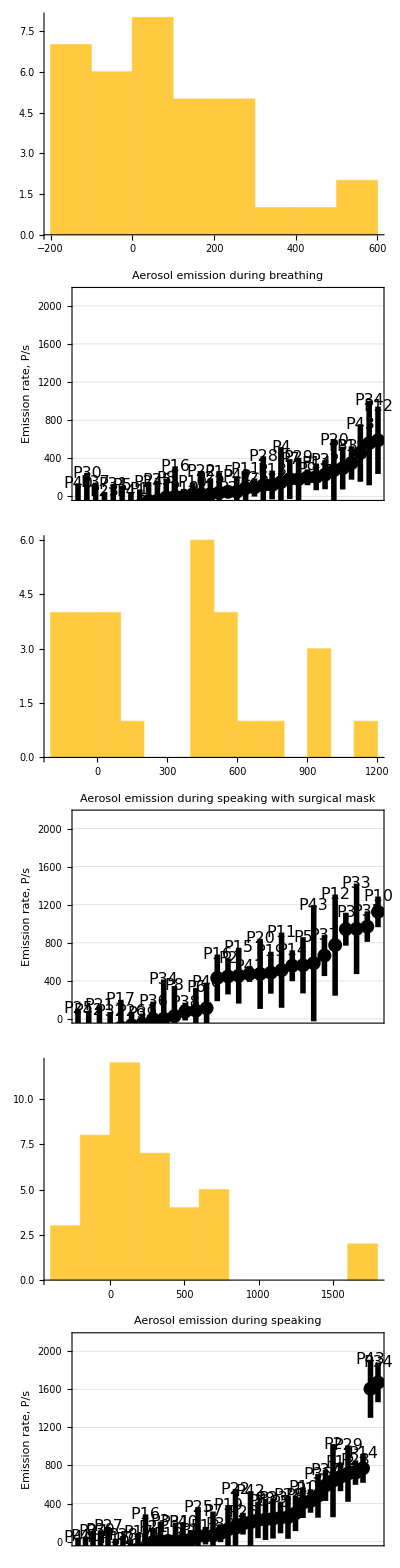

```mathematica
Column[Join@@TaskPlot/@(Measurements/.ToEnglish)]
```

```mathematica
Clear[R,TaskPlotWater]

R = 27;

TaskPlotWater[task_?StringQ] := Module[{A,D,G,h,i},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Wasseremission (mg/s)","Proband"}/.ToEnglish],2];
A = Select[A,NumericQ[#[[1]]]&];
If[A=={},Return[2]];
A = SortBy[A,First];
i = 0;
D = Map[{
Point[h={++i,#[[1]]}],
Text@@Prepend[
If[MemberQ[{ (* "Playing" *) },task],
{h,{0,   3}},
{h,{0,-3}}],
Style[
StringDrop[#[[2]],0],
FontColor->GrayLevel[0],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*2/3]]]
}&,A];
G = Graphics[
{AbsolutePointSize[10],D},
AspectRatio->0.4,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{None,"mg/s"},
FrameTicks->{None,Automatic},
GridLines  ->{None,Automatic},
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Water emission during ",ToLowerCase[task]],
PlotRange->{All,{0,R}},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"TaskPlots\\mg-s\\",task,"_Water.tif"],
Rasterize[G],
"ImageEncoding"->"LZW"]];

Put[
{First/@A,G},
StringJoin[OutPath,"TaskPlots\\mg-s\\",task,"_Water.dat"]];

G];
```

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Breathing_Water.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Speaking With Surgical Mask_Water.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\mg-s\Speaking_Water.tif

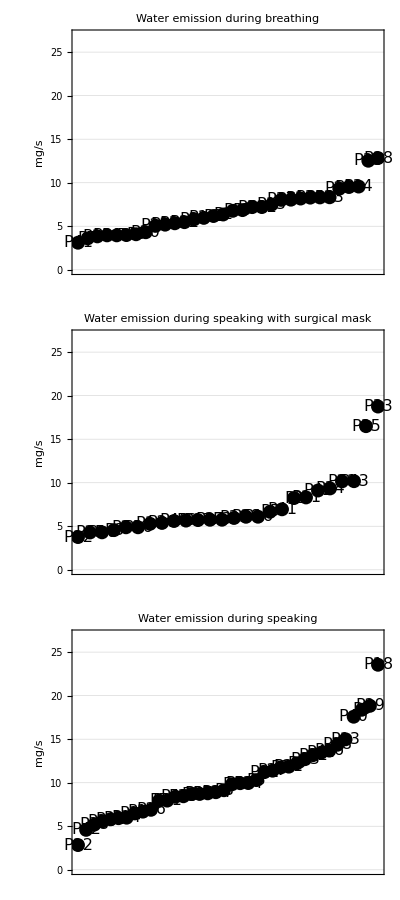

```mathematica
Column[TaskPlotWater/@Measurements]
```

```mathematica
Clear[R,TaskPlotPerWater]

R = {0,400};

TaskPlotPerWater[task_?StringQ] := Module[{A,D,G,h,i},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Partikel/Wasser (P/mg)","ER σ (P/s)","Emissionsrate (P/s)","Proband"}/.ToEnglish],2];
A = Select[A,NumericQ[#[[1]]]&];
If[A=={},Return[2]];
A = Transpose[A];
A[[2]] *= A[[1]]/A[[3]];
A[[2]] = Abs[A[[2]]];
A = Drop[A,{3}];
A = Transpose[A];
A = SortBy[A,First];
i = 0;
D = Map[(
++i;
{Point[{i,#[[1]]}],
Line[h={
{i,Max[-Infinity,#[[1]]-#[[2]]]},
{i,                                  #[[1]]+#[[2]]   }}],
Text@@Prepend[
If[MemberQ[{ (* "Playing" *) },task],
{h[[1]],{0,   2}},
{h[[2]],{0,-2}}],
Style[
StringDrop[#[[3]],0],
FontColor->GrayLevel[0],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*2/3]]]}
)&,A];
D = Flatten[D];
G = Graphics[
Join[
{AbsoluteThickness[  4],
AbsolutePointSize[10]},
D],
AspectRatio->0.4,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{None,"Particles / Water,   P/mg"},
FrameTicks->{None,Automatic},
GridLines  ->{None,Automatic},
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->StringJoin["Aerosol emission during ",ToLowerCase[task]],
PlotRange->{All,R},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"TaskPlots\\P-mg\\",task,"_PerWater.tif"],
Rasterize[G],
"ImageEncoding"->"LZW"]];

Put[
{NormalDistribution@@@Map[N[#[[{1,2}]]]&,A],G},
StringJoin[OutPath,"TaskPlots\\P-mg\\",task,"_PerWater.dat"]];

G];
```

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Breathing_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Speaking With Surgical Mask_PerWater.tif

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\TaskPlots\P-mg\Speaking_PerWater.tif

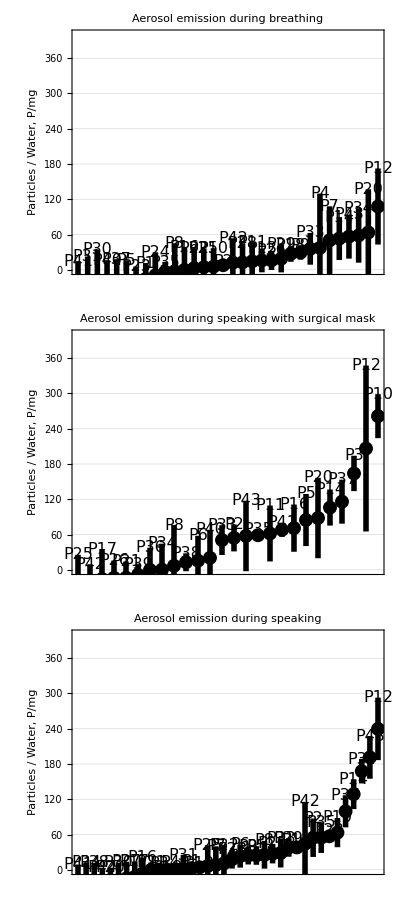

```mathematica
Column[TaskPlotPerWater/@Measurements]
```

```mathematica
Clear[R,CorrPlotPerWater,
A,a,c,p]

R = {0,370};

CorrPlotPerWater[
instr_?StringQ,
        X_?StringQ,
        Y_?StringQ] := Module[{A,B,a,c,p},
A = SelectRows[Z,"Instrument"/.ToEnglish,(#==(instr/.ToEnglish))&];
If[a=(Length[A]==2),A = Z];
A = {
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(X/.ToEnglish))&],
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(Y/.ToEnglish))&]};
If[Min[Length/@A]==2,Return[2]];
A = Map[Drop[ExtractColumn[#,{"Proband","Partikel/Wasser (P/mg)","ER σ (P/s)","Emissionsrate (P/s)"}/.ToEnglish],2]&,A];
A = Map[Select[#,NumericQ[#[[2]]]&]&,A];
If[Min[Length/@A]==0,Return[3]];
A = Map[{#[[1]],#[[2]],#[[2]]*#[[3]]/#[[4]]}&,A,{2}];
A = MyMerge[A[[1]],A[[2]],1,True];
If[A=={},Return[4]];
B = Map[{MultinormalDistribution[{#[[2,1,1]],#[[2,2,1]]},{{#[[2,1,2]]^2,0},{0,#[[2,2,2]]^2}}],#[[1]]}&,A];
p = Map[StringDrop[#,1]&,First/@A];
p = SortBy[p,ToExpression];
p = ConcatStringList[p,", "];
p = StringJoin[p,"  (n = ",ToString[Length[A]],")"];
A = Last/@A;
A = Transpose/@A;
c = Y/.{
"Atmen"                                       ->Hue[2/3,0.6,1],
"Sprechen mit MNS"              ->Hue[1/3,0.4,0.9],
"Sprechen"                                ->Hue[1/3,1.0,0.8],
"Musikspiel mit Schutz"  ->Hue[0/3,0.4,1],
"Musikspiel"                           ->Hue[0/3,1.0,1],
"Luftreiniger"                       ->PatternFilling["Hexagon",ImageScaled[0.008]],
"Messbereich"                         ->GrayLevel[0.7],
"Proband im Messbereich"->GrayLevel[0.9],
"Ventilator"                           ->PatternFilling["Chevron",ImageScaled[0.005]]};

A = Graphics[
{If[True,
{AbsoluteThickness[5],GrayLevel[0.9],
If[ListQ[R],
Line[{{0,0},ConstantArray[Last[R],2]}],
If[NumericQ[R],
Line[{{0,0},ConstantArray[R,2]}],
Nothing]]},
Nothing],
Text[
Style[If[a,"",p],
FontColor->GrayLevel[0.5],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->24],
Scaled[{0.94,0.98}],
{1,1}],
AbsoluteThickness[1],
c                     ,Circle@@@A,
Opacity[0.2],Disk@@@A},
AspectRatio->If[R===All,1,Automatic],
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{
StringJoin["Emission during ",ToLowerCase[X/.ToEnglish],",   P/mg water"],
StringJoin["Emission during ",ToLowerCase[Y/.ToEnglish],",   P/mg water"]},
GridLines->Automatic,
ImageSize->1000,
LabelStyle->MyTS,
(*
PlotLabel->instr/.{"Alle"->"All","Kl"->"Clarinet","KP"->"Singing","Ob"->"Oboe","Qu"->"Flute","Tr"->"Trumpet"},
*)
PlotRange->{R,R},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"CorrPlots\\P-mg\\",instr,"~",Y,"(",X,")_PerWater.tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];

Put[{B,A},StringJoin[OutPath,"CorrPlots\\P-mg\\",instr,"~",Y,"(",X,")_PerWater.dat"]];

A];

(*
CorrPlotPerWater["Alle","Atmen","Sprechen"]
*)
```

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Sprechen mit MNS(Atmen)_PerWater.tif

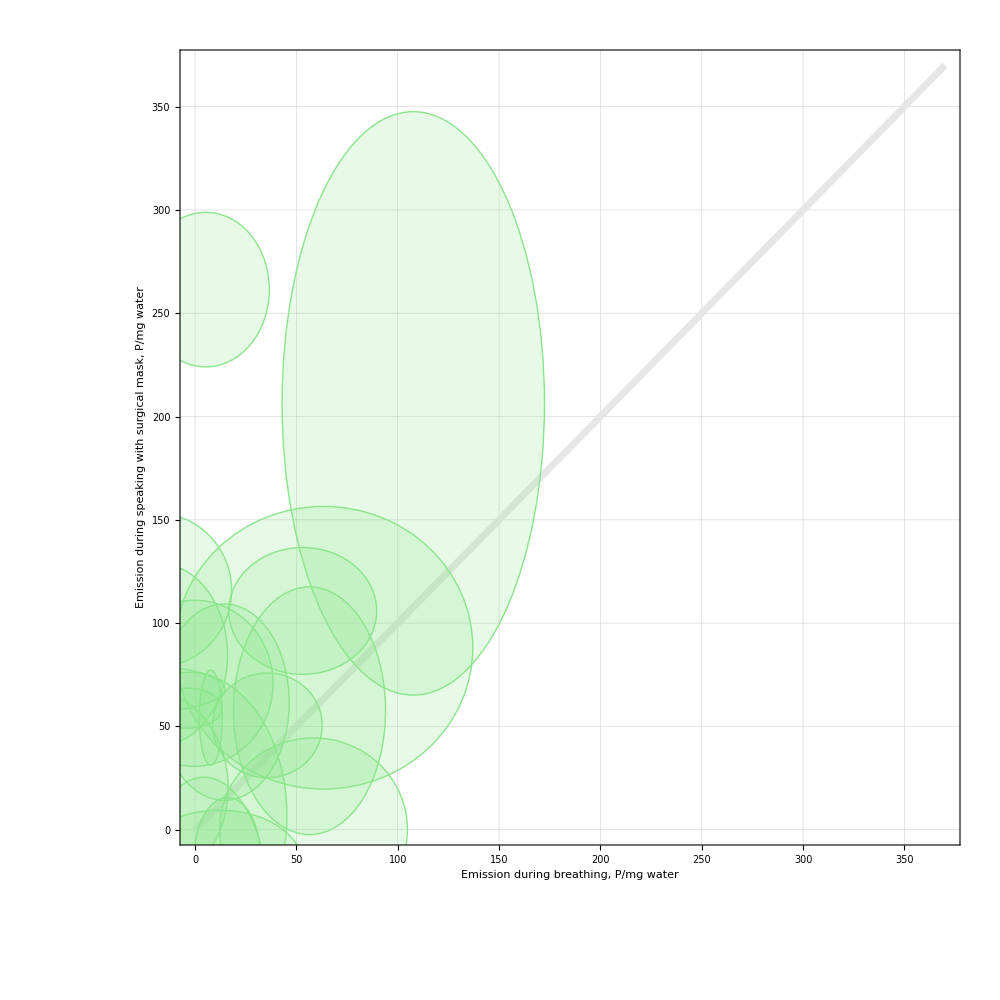

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Sprechen(Atmen)_PerWater.tif

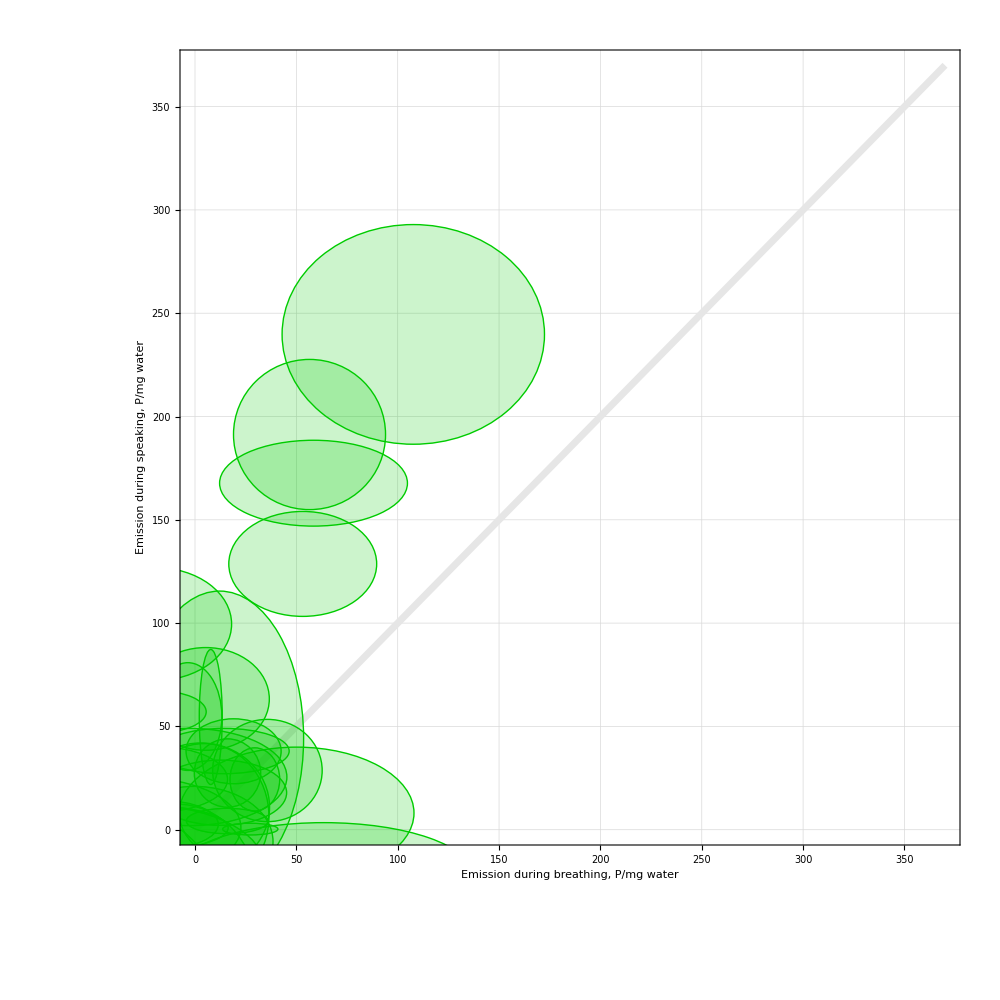

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-mg\Alle~Sprechen(Sprechen mit MNS)_PerWater.tif

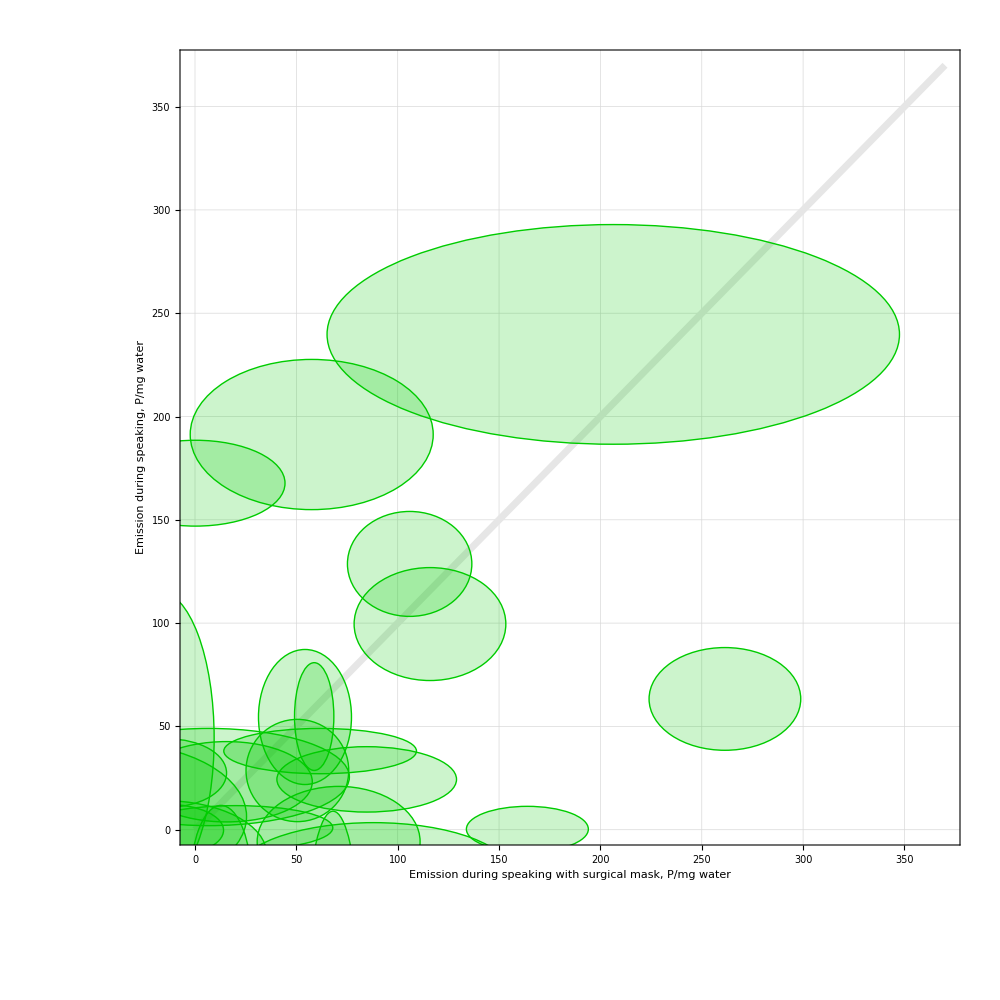

```mathematica
CorrPlotPerWater["Alle","Atmen","Sprechen mit MNS"                           ]
CorrPlotPerWater["Alle","Atmen",                                             "Sprechen"]
CorrPlotPerWater["Alle",                    "Sprechen mit MNS","Sprechen"]
```

```mathematica
Clear[R,CorrPlotWater,
A,a,c,g,p,s,x,α]

R = 25;

CorrPlotWater[
instr_?StringQ,
        X_?StringQ,
        Y_?StringQ] := Module[{A,B,a,c,g,p,s,x,α},
A = SelectRows[Z,"Instrument"/.ToEnglish,(#==(instr/.ToEnglish))&];
If[a=(Length[A]==2),A = Z];
A = {
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(X/.ToEnglish))&],
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(Y/.ToEnglish))&]};
If[Min[Length/@A]==2,Return[2]];
A = Map[Drop[ExtractColumn[#,{"Proband","Wasseremission (mg/s)"}/.ToEnglish],2]&,A];
A = Map[Select[#,NumericQ[#[[2]]]&]&,A];
If[Min[Length/@A]==0,Return[3]];
A = MyMerge[A[[1]],A[[2]],1,True];
If[A=={},Return[4]];
B = Map[{Flatten[#[[2]]],#[[1]]}&,A];
p = Map[StringDrop[#,1]&,First/@A];
p = SortBy[p,ToExpression];
p = ConcatStringList[p,", "];
p = StringJoin[p,"  (n = ",ToString[Length[A]],")"];
A = Last/@A;
A = Transpose/@A;
A = Flatten[A,1];
g = Map[({Cos[α],Sin[α]}.#)&,A];
g = NMinimize[g.g,α];
g = α/.g[[2]];
g = Tan[g+π/2];

{x,y} = Transpose[A];
Print[Correlation[x,y]];
x -= Mean[x];
y -= Mean[y];
Print[(x.y)/Sqrt[x.x*y.y]];

A = Point[A];
c = Y/.{
"Atmen"                                       ->Hue[2/3,0.6,1],
"Sprechen mit MNS"              ->Hue[1/3,0.4,0.9],
"Sprechen"                                ->Hue[1/3,1.0,0.8],
"Musikspiel mit Schutz"  ->Hue[0/3,0.4,1],
"Musikspiel"                           ->Hue[0/3,1.0,1],
"Luftreiniger"                       ->PatternFilling["Hexagon",ImageScaled[0.008]],
"Messbereich"                         ->GrayLevel[0.7],
"Proband im Messbereich"->GrayLevel[0.9],
"Ventilator"                           ->PatternFilling["Chevron",ImageScaled[0.005]]};
s = {
FontColor->GrayLevel[0.5],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*5/6]};
A = Graphics[
{Text[Style@@Prepend[s,If[a,"",p]                                                        ],Scaled[  0.98*{1,1}],{1,1}],
Text[Style@@Prepend[s,StringJoin["f = ",RealForm[g,4,2]]],Scaled[{0.98,0.94} ],{1,1}],
If[NumericQ[R],
{AbsoluteThickness[5],
GrayLevel[0.9],
Line[Transpose[{#,g*#}]&[
{0,0.93*R*Min[1,1/g]}]]},
Nothing],
AbsolutePointSize[20],c,A},
AspectRatio->If[R===All,1,Automatic],
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{
StringJoin["Water emission during ",ToLowerCase[X/.ToEnglish],",   mg/s"],
StringJoin["Water emission during ",ToLowerCase[Y/.ToEnglish],",   mg/s"]},
GridLines->Automatic,
ImageSize->1000,
LabelStyle->MyTS,
(*
PlotLabel->instr/.{"Alle"->"All","Kl"->"Clarinet","KP"->"Singing","Ob"->"Oboe","Qu"->"Flute","Tr"->"Trumpet"},
*)
PlotRange->{{0,R},{0,R}},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"CorrPlots\\mg-s\\",instr,"~",Y,"(",X,")_Water.tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];

Put[{B,A},StringJoin[OutPath,"CorrPlots\\mg-s\\",instr,"~",Y,"(",X,")_Water.dat"]];

A];

(*
CorrPlotWater["Alle","Atmen","Sprechen"]
*)
```

0.61826

0.61826

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Sprechen mit MNS(Atmen)_Water.tif

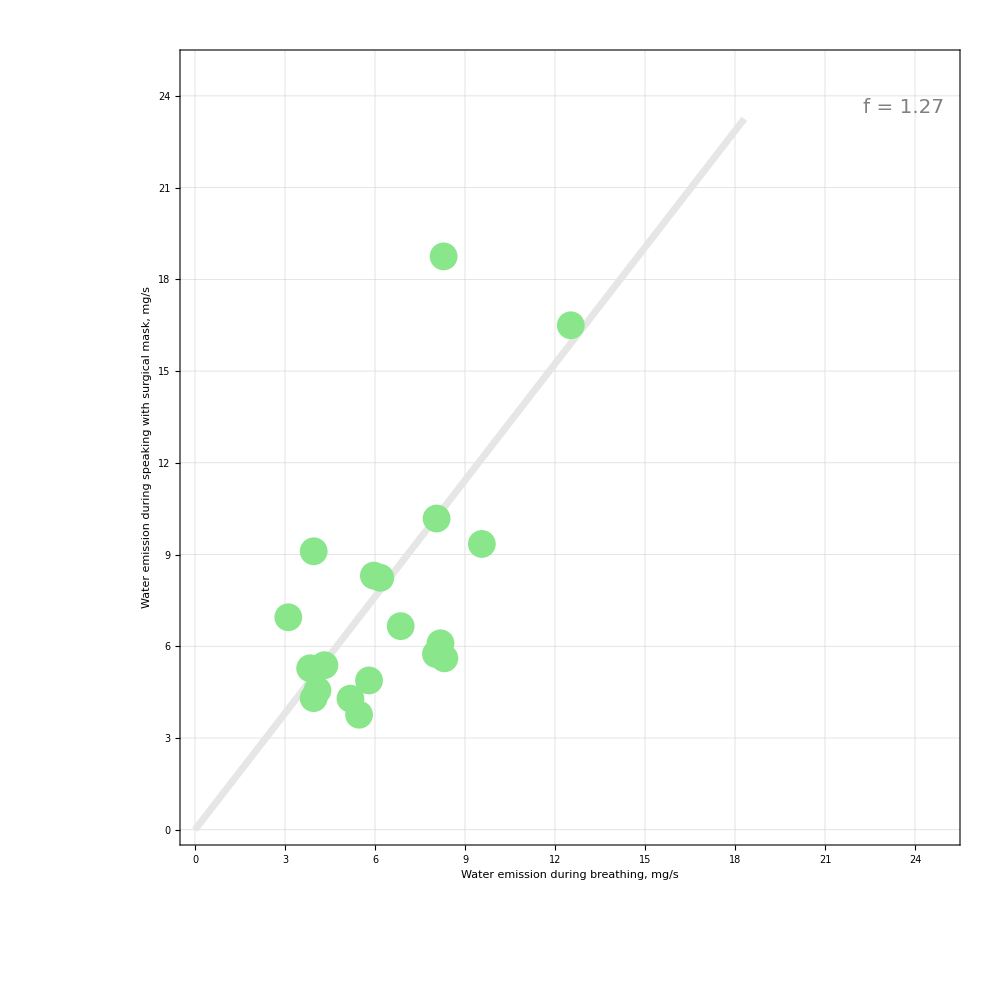

0.666113

0.666113

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Sprechen(Atmen)_Water.tif

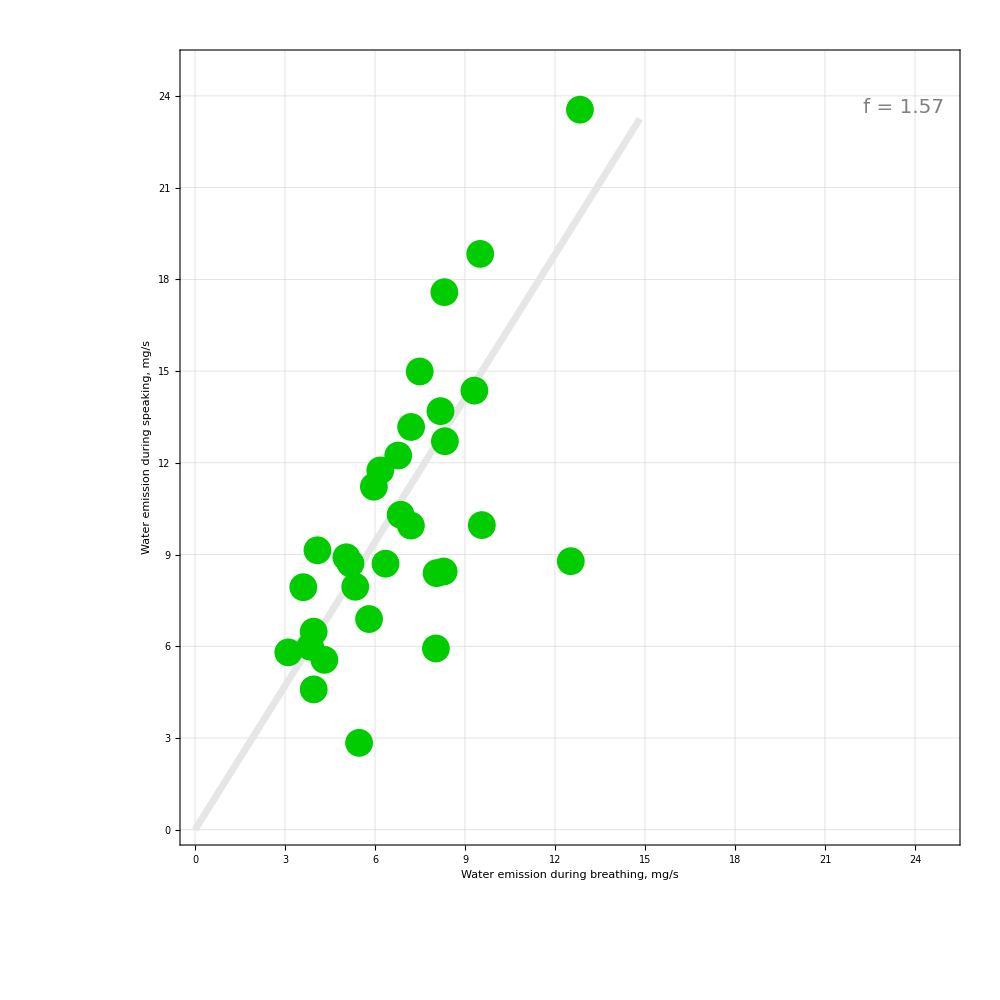

0.0680885

0.0680885

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\mg-s\Alle~Sprechen(Sprechen mit MNS)_Water.tif

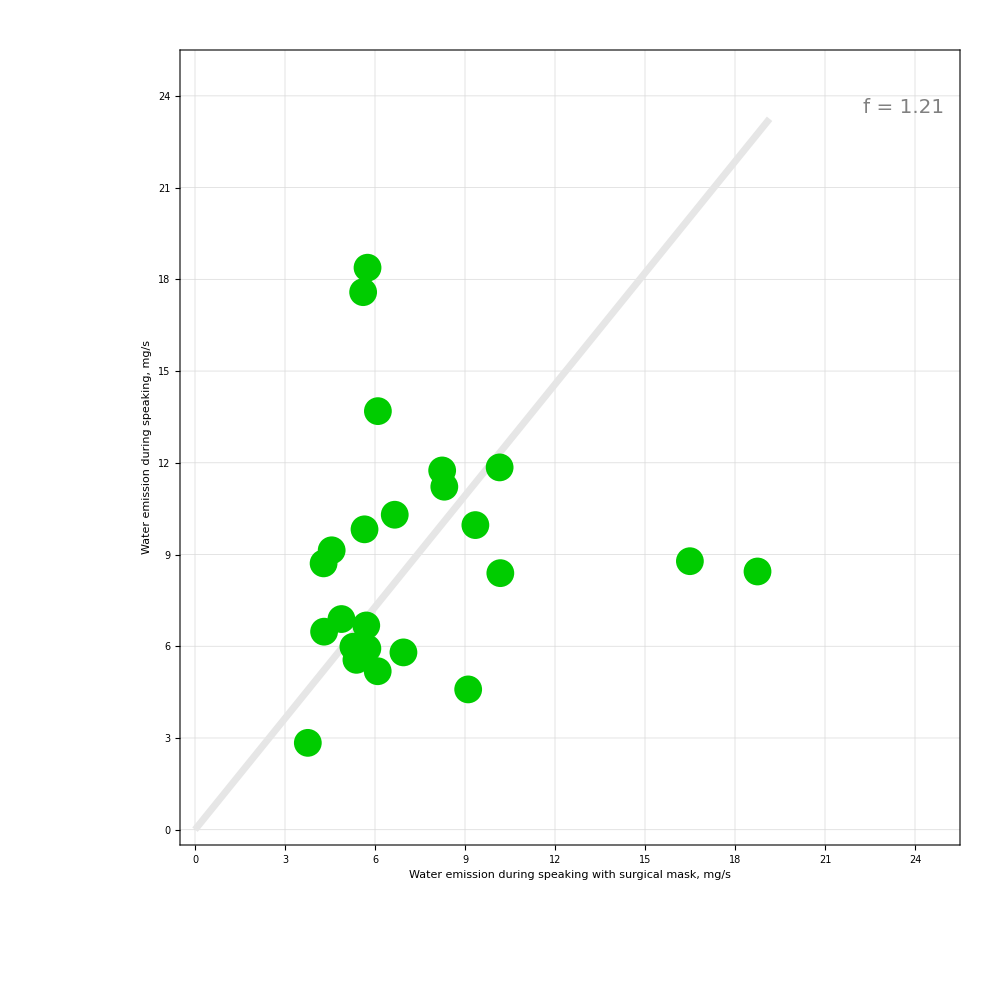

```mathematica
CorrPlotWater["Alle","Atmen","Sprechen mit MNS"                           ]
CorrPlotWater["Alle","Atmen",                                             "Sprechen"]
CorrPlotWater["Alle",                    "Sprechen mit MNS","Sprechen"]
```

```mathematica
Clear[R,CorrPlot,
A,a,c,p]

R = {0,2000};

CorrPlot[
instr_?StringQ,
        X_?StringQ,
        Y_?StringQ] := Module[{A,B,a,c,p},
A = SelectRows[Z,"Instrument"/.ToEnglish,(#==(instr/.ToEnglish))&];
If[a=(Length[A]==2),A = Z];
A = {
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(X/.ToEnglish))&],
SelectRows[A,"Aufgabe"/.ToEnglish,(#==(Y/.ToEnglish))&]};
If[Min[Length/@A]==2,Return[2]];
A = Map[Drop[ExtractColumn[#,{"Proband","Emissionsrate (P/s)","ER σ (P/s)"}/.ToEnglish],2]&,A];
A = MyMerge[A[[1]],A[[2]],1,True];
If[A=={},Return[3]];
B = Map[{MultinormalDistribution[{#[[2,1,1]],#[[2,2,1]]},{{#[[2,1,2]]^2,0},{0,#[[2,2,2]]^2}}],#[[1]]}&,A];
p = Map[StringDrop[#,1]&,First/@A];
p = SortBy[p,ToExpression];
p = ConcatStringList[p,", "];
p = StringJoin[p,"  (n = ",ToString[Length[A]],")"];
A = Last/@A;
A = Transpose/@A;
c = Y/.{
"Atmen"                                       ->Hue[2/3,0.6,1],
"Sprechen mit MNS"              ->Hue[1/3,0.4,0.9],
"Sprechen"                                ->Hue[1/3,1.0,0.8],
"Musikspiel mit Schutz"  ->Hue[0/3,0.4,1],
"Musikspiel"                           ->Hue[0/3,1.0,1],
"Luftreiniger"                       ->PatternFilling["Hexagon",ImageScaled[0.008]],
"Messbereich"                         ->GrayLevel[0.7],
"Proband im Messbereich"->GrayLevel[0.9],
"Ventilator"                           ->PatternFilling["Chevron",ImageScaled[0.005]]};
A = Graphics[
{If[True,
{AbsoluteThickness[5],GrayLevel[0.8],
If[ListQ[R],
Line[{{0,0},ConstantArray[Last[R],2]}],
If[NumericQ[R],
Line[{{0,0},ConstantArray[R,2]}],
Nothing]]},
Nothing],
Text[
Style[If[a,"",p],
FontColor->GrayLevel[0.5],
FontFamily->"Arial",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->Round[(FontSize/.MyTS)*5/6]],
Scaled[{0.94,0.98}],
{1,1}],
AbsoluteThickness[1],
c                     ,Circle@@@A,
Opacity[0.2],Disk@@@A},
AspectRatio->If[R===All,1,Automatic],
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{
StringJoin["Emission rate during ",ToLowerCase[X/.ToEnglish],",  P/s"],
StringJoin["Emission rate during ",ToLowerCase[Y/.ToEnglish],",  P/s"]},
GridLines->Automatic,
ImageSize->1000,
LabelStyle->MyTS,
(*
PlotLabel->instr/.{"Alle"->"All","Kl"->"Clarinet","KP"->"Singing","Ob"->"Oboe","Qu"->"Flute","Tr"->"Trumpet"},
*)
PlotRange->{R,R},
PlotRangeClipping->True];

Print[
MDExport[
StringJoin[OutPath,"CorrPlots\\P-s\\",instr,"~",Y,"(",X,").tif"],
Rasterize[A],
"ImageEncoding"->"LZW"]];

Put[{B,A},StringJoin[OutPath,"CorrPlots\\P-s\\",instr,"~",Y,"(",X,").dat"]];

A];

(*
CorrPlot["Alle","Atmen","Sprechen"]
*)
```

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Sprechen mit MNS(Atmen).tif

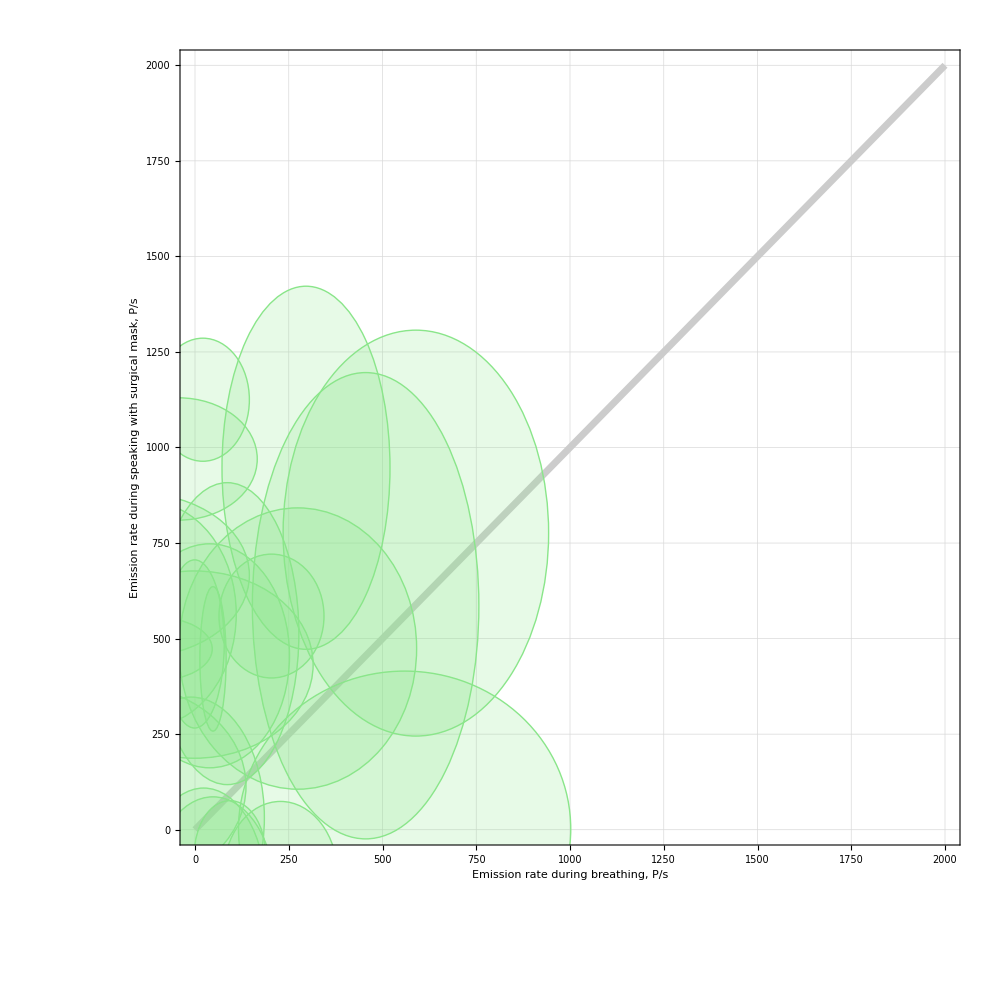

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Sprechen(Atmen).tif

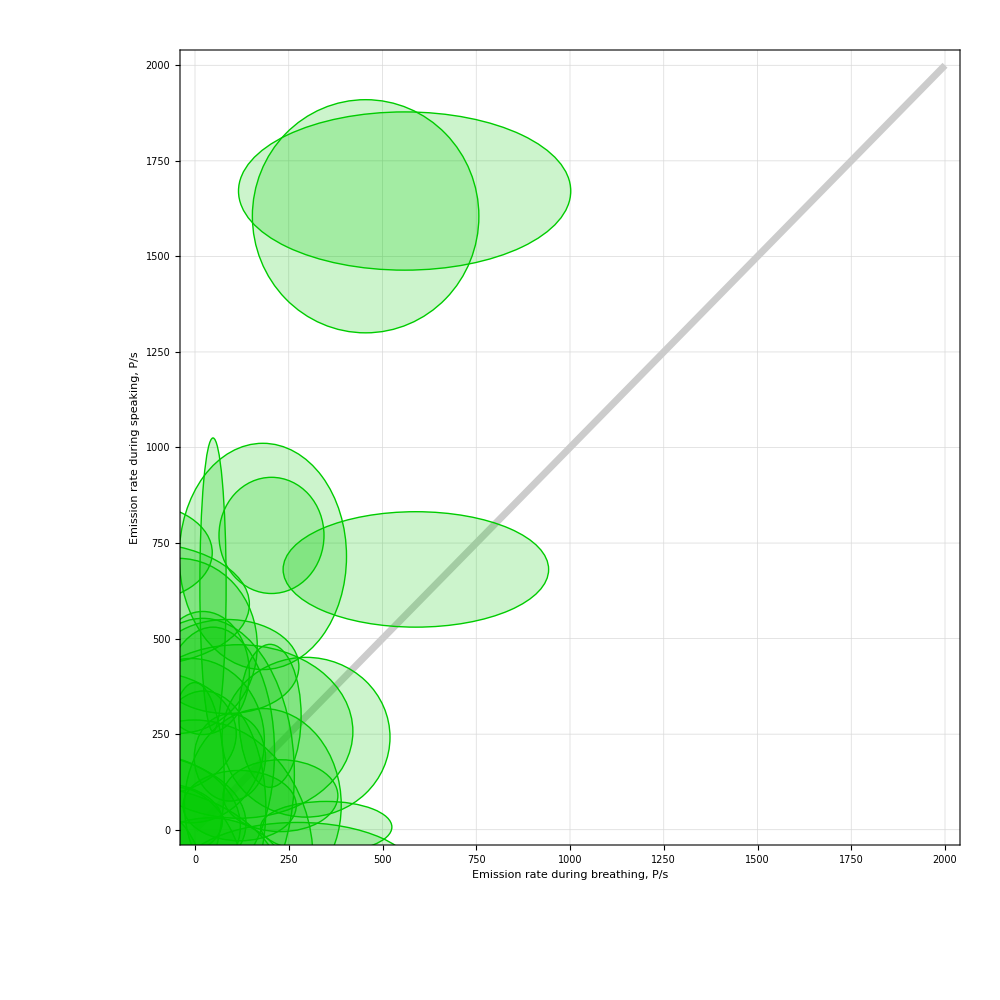

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\CorrPlots\P-s\Alle~Sprechen(Sprechen mit MNS).tif

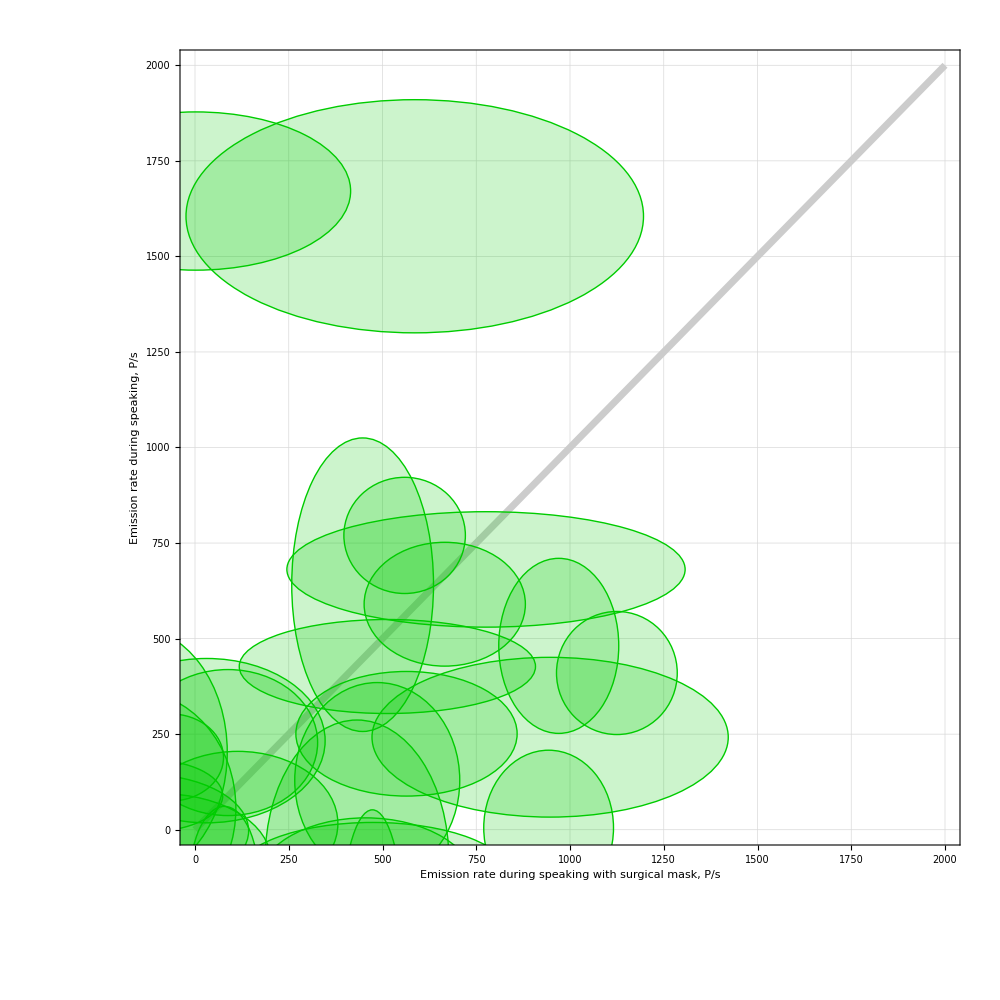

```mathematica
CorrPlot["Alle","Atmen","Sprechen mit MNS"                           ]
CorrPlot["Alle","Atmen",                                             "Sprechen"]
CorrPlot["Alle",                    "Sprechen mit MNS","Sprechen"]
```

```mathematica
StringJoin[OutPath,"PlotData.dat"];
Put[Z,%]
```

```mathematica
(*
                      ENDE.
*)
```